# Flow of energy in the gravitational field

```mathematica
(*Define the physical constants*)G=1;c=1;(*gravitational constant in m^3 kg^-1 s^-2*)m=1.0;(*mass of each point in kg*)r=1.0;(*distance of each point from the origin in m*)(*Define the positions of the two point masses*)r1={-r,0,0};
r2={r,0,0};
(*Define the spin of each BH*)L1={0,0,1};L2={0,0,1};(*Need to add angular momentum due to black holes orbiting at Kepler angular veloctiy*)

(*Define the gravitational field of a point mass at a given position*)
Eg[point_,r_]:=-G*m/Norm[point-r]^3*(point-r);
Bg[point_,r_,L_]:=G/(2 c^2) L/Norm[point-r]^3;

(*Define the total gravitational field as the sum of the fields from the two points*)
totalField[point_]:=Eg[point,r1]+Eg[point,r2]+Bg[point,r1,L1]+Bg[point,r2,L2];

(*Create a 3D vector plot of the field*)
VectorPlot3D[totalField[{x,y,z}],{x,-2*r,2*r},{y,-2*r,2*r},{z,-2*r,2*r},VectorColorFunction->"Rainbow",PlotLegends->Automatic,VectorScaling->Automatic]
```

-Graphics3D-

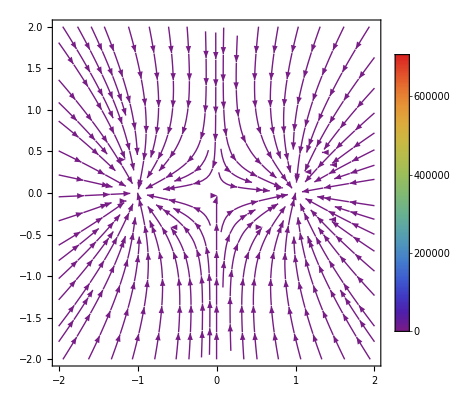

```mathematica
(*Existing code up to totalField definition*)(*Create a 2D stream plot of the field in the xy-plane*)StreamPlot[{totalField[{x,y,0}][[1]],totalField[{x,y,0}][[2]]},{x,-2*r,2*r},{y,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
(*Now define the Poynting vector*)
Sg[point_]:=-c^2/(π G)Cross[(Eg[point,r1]+Eg[point,r2]),Bg[point,r1,L1]+Bg[point,r2,L2]];
```

```mathematica
VectorPlot3D[Sg[{x,y,z}],{x,-2*r,2*r},{y,-2*r,2*r},{z,-2*r,2*r},VectorColorFunction->"Rainbow",PlotLegends->Automatic,VectorScaling->Automatic,PlotLabel->Style["3D vector plot of Poynting vector",Black,20],AxesLabel->{x,y,z}]
```

OptionValue::nodef: Unknown option ListVectorData for System`VectorPlotsDump`ComputeVectorPoints.

-Graphics3D-

OptionValue::optnf: Option name ListVectorData not found in defaults for System`VectorPlotsDump`ComputeVectorPoints.

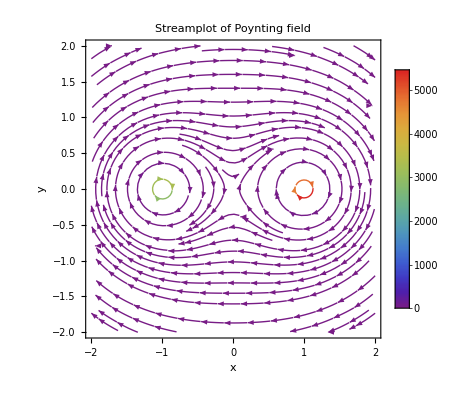

```mathematica
StreamPlot[{Sg[{x,y,0}][[1]],Sg[{x,y,0}][[2]]},{x,-2*r,2*r},{y,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic,PlotLabel->Style["Streamplot of Poynting field",Black,20],Axes->True,AxesLabel->{x,y}]
```

```mathematica
Sg[{x,0,z}]
```

{0.,-(0.-0.5/((Abs[-1+x]^2+Abs[z]^2)^3)+(0.5 x)/((Abs[-1+x]^2+Abs[z]^2)^3)+0.5/((Abs[1+x]^2+Abs[z]^2)^3)+(0.5 x)/((Abs[1+x]^2+Abs[z]^2)^3)+(1. x)/((Abs[-1+x]^2+Abs[z]^2)^(3/2) (Abs[1+x]^2+Abs[z]^2)^(3/2)))/π,0.}

```mathematica
Sgy[x_,z_]=Sg[{x,0,z}][[2]];
(*Define a range and grid spacing for x and z*)xRange={-2,2};
zRange={-2,2};
gridSpacing=0.1;

(*Generate the 2D grid in xz-plane*)
grid=Flatten[Table[{x,z},{x,xRange[[1]],xRange[[2]],gridSpacing},{z,zRange[[1]],zRange[[2]],gridSpacing}],1];

(*Generate graphics primitives for each point in the grid*)
graphics=Map[{ColorData["Rainbow"][Rescale[Sgy[#],{-1,1}]],PointSize[0.015],Point[#]}&,grid];

(*Display the graphics*)
Graphics[graphics,Axes->True,PlotRange->{xRange,zRange},AxesLabel->{x,z}]
```

-Graphics-

```mathematica
(*Define the physical constants and other parameters as before*)...
(*Use DensityPlot to visualize Sgy in the xz-plane*)
DensityPlot[Sg[{x,0,z}][[2]],{x,xRange[[1]],xRange[[2]]},{z,zRange[[1]],zRange[[2]]},ColorFunction->"Rainbow",PlotLegends->Automatic,AxesLabel->{"x","z"},,Epilog->{PointSize[0.025],Point[r1[[{1,3}]]],Point[r2[[{1,3}]]]}]
```

```mathematica
zRange
```

{-2,2}

```mathematica
r2[[{1,3}]]
```

{1,0}

```mathematica
Sg[{x,0,z}][[2]]
```

-(0.-0.5/((Abs[-1+x]^2+Abs[z]^2)^3)+(0.5 x)/((Abs[-1+x]^2+Abs[z]^2)^3)+0.5/((Abs[1+x]^2+Abs[z]^2)^3)+(0.5 x)/((Abs[1+x]^2+Abs[z]^2)^3)+(1. x)/((Abs[-1+x]^2+Abs[z]^2)^(3/2) (Abs[1+x]^2+Abs[z]^2)^(3/2)))/π

```mathematica
StreamPlot[{Sg[{x,0,z}][[1]],Sg[{x,0,z}][[3]]},{x,-2*r,2*r},{z,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic,PlotLabel->Style["Streamplot of Poynting field (xz plane)",Black,20],Axes->True,AxesLabel->{x,z}]
```

OptionValue::optnf: Option name ListVectorData not found in defaults for System`VectorPlotsDump`ComputeVectorPoints.

-Graphics-

```mathematica
(*2D stream plots for different values of z*)GraphicsRow[{StreamPlot[{Sfield[{x,y,-0.1}][[1]],Sfield[{x,y,-0.1}][[2]]},{x,-2*r,2*r},{y,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic],StreamPlot[{Sfield[{x,y,0}][[1]],Sfield[{x,y,0}][[2]]},{x,-2*r,2*r},{y,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic],StreamPlot[{Sfield[{x,y,1}][[1]],Sfield[{x,y,1}][[2]]},{x,-2*r,2*r},{y,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic]}]
```

Part::partw: Part 2 of Sfield[{x,y,-0.1}] does not exist.

Part::partw: Part 2 of Sfield[{-1.99971,-1.99971,-0.1}] does not exist.

Part::partw: Part 2 of Sfield[{-1.714,-1.99971,-0.1}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
(*Constants*)μ0=4 π 10^-7;
m1={1,0,0};(*Magnetic moment of the first magnet*)m2={1,0,0};(*Magnetic moment of the second magnet*)r1={-1,0,0};(*Position of the first magnet*)r2={1,0,0};(*Position of the second magnet*)(*Magnetic field of a dipole at a given position*)Bfield[point_,r_,m_]:=μ0/(4 π) (3 (point-r).m (point-r)/Norm[point-r]^5-m/Norm[point-r]^3);

(*Electric field at a given position-This needs to be defined*)
Efield[point_]:={0,0,0};(*Example:No electric field*)(*Poynting vector at a given position*)Sfield[point_]:=Efield[point]×(Bfield[point,r1,m1]+Bfield[point,r2,m2]);

(*3D vector plot of the Poynting vector field*)
VectorPlot3D[Sfield[{x,y,z}],{x,-2,2},{y,-2,2},{z,-2,2},VectorColorFunction->"Rainbow",PlotLegends->Automatic,VectorScaling->Automatic]
```

-Graphics3D-

```mathematica
(*Constants*)μ0=1;
ε0=1;
q=-1;(*Charge at each location*)m1={1,0,0};(*Magnetic moment of the first magnet*)m2={1,0,0};(*Magnetic moment of the second magnet*)r1={-1,0,0};(*Position of the first magnet*)r2={1,0,0};(*Position of the second magnet*)(*Magnetic field of a dipole at a given position*)Bfield[point_,r_,m_]:=μ0/(4 π) (3 (point-r).m (point-r)/Norm[point-r]^5-m/Norm[point-r]^3);

(*Electric field of a point charge at a given position*)
EfieldCharge[point_,r_,q_]:=(1/(4 π ε0)) q (point-r)/Norm[point-r]^3;

(*Total electric field at a given position*)
Efield[point_]:=EfieldCharge[point,r1,q]+EfieldCharge[point,r2,q];

(*Poynting vector at a given position*)
Sfield[point_]:=Efield[point]×(Bfield[point,r1,m1]+Bfield[point,r2,m2]);

(*3D vector plot of the Poynting vector field*)
VectorPlot3D[Sfield[{x,y,z}],{x,-2,2},{y,-2,2},{z,-2,2},VectorColorFunction->"Rainbow",PlotLegends->Automatic,VectorScaling->Automatic]
```

-Graphics3D-

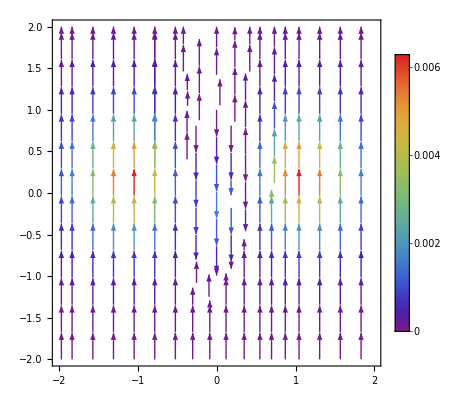

```mathematica
StreamPlot[{Sfield[{x,y,1}][[1]],Sfield[{x,y,1}][[2]]},{x,-2*r,2*r},{y,-2*r,2*r},StreamColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
maxvectorsize=2;
```

```mathematica
VectorPlot[Sg[x,y,0],{x,-2,2},{y,-2,2},VectorScale->{Automatic,Automatic,If[#5>maxvectorsize,maxvectorsize,#5]&},VectorPoints->{40,40},StreamPoints->Coarse,StreamStyle->"Line"]
```

VectorPlot::nonopt: Options expected (instead of StreamStyle→Line) beyond position 3 in VectorPlot[Sg[x,y,0],{x,-2,2},{y,-2,2},VectorScale→{Automatic,Automatic,If[#5>maxvectorsize,maxvectorsize,#5]&},VectorPoints→{40,40},StreamPoints→Coarse,StreamStyle→Line]. An option must be a rule or a list of rules.

VectorPlot[Sg[x,y,0],{x,-2,2},{y,-2,2},VectorScale→{Automatic,Automatic,If[#5>maxvectorsize,maxvectorsize,#5]&},VectorPoints→{40,40},StreamPoints→Coarse,StreamStyle→Line]

```mathematica
(*Constants and Definitions*)(*... Include previous definitions of Bfield,EfieldCharge,Efield,and Sfield here...*)maxvectorsize=∞;(*Define maxvectorsize value*)(*2D vector plots for different values of z*)GraphicsRow[{VectorPlot[Sfield[{x,y,-0.1}],{x,-2,2},{y,-2,2},VectorScale->{Automatic,Automatic,If[#5>maxvectorsize,maxvectorsize,#5]&},VectorPoints->{40,40},StreamPoints->Coarse,StreamStyle->"Line"],VectorPlot[Sfield[{x,y,0}],{x,-2,2},{y,-2,2},VectorScale->{Automatic,Automatic,If[#5>maxvectorsize,maxvectorsize,#5]&},VectorPoints->{40,40},StreamPoints->Coarse,StreamStyle->"Line"],VectorPlot[Sfield[{x,y,1}],{x,-2,2},{y,-2,2},VectorScale->{Automatic,Automatic,If[#5>maxvectorsize,maxvectorsize,#5]&},VectorPoints->{40,40},StreamPoints->Coarse,StreamStyle->"Line"]}]
```

-Graphics-